```mathematica
Get["lions.mx"]
```

```mathematica
lions//Length
```

800

```mathematica
RandomSample[lions,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Get["tigers.mx"]
```

```mathematica
tigers//Length
```

800

```mathematica
RandomSample[tigers,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Get["bears.mx"]
```

```mathematica
bears//Length
```

800

```mathematica
RandomSample[bears,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
800+800+800
```

2400

```mathematica
data=RandomSample[
Flatten[{
Map[#->"lion"&,lions],
Map[#->"tiger"&,tigers],
Map[#->"bear"&,bears]
}]
];
```

```mathematica
Take[data,5]
```

{-Graphics-→lion,-Graphics-→bear,-Graphics-→bear,-Graphics-→lion,-Graphics-→tiger}

```mathematica
Length[data]
```

2400

```mathematica
training=Take[data,2200];
validation=Take[data,-200];
```

```mathematica
RandomSample[training,5]
```

{-Graphics-→tiger,-Graphics-→tiger,-Graphics-→lion,-Graphics-→tiger,-Graphics-→bear}

```mathematica
RandomSample[validation,5]
```

{-Graphics-→lion,-Graphics-→tiger,-Graphics-→lion,-Graphics-→bear,-Graphics-→lion}

```mathematica
net=NetGraph[<|
"convolution"->ConvolutionLayer[80,7],
"ramp"->ElementwiseLayer[Ramp],
"pool"->PoolingLayer[5,3],
"flatten"->FlattenLayer[],
"connect"->DotPlusLayer[3],
"softmax"->SoftmaxLayer[]
|>,
{"convolution"->"ramp"->"pool"->"flatten"->"connect"->"softmax"},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"lion","tiger","bear"}}]
]
```

NetGraph[]

```mathematica
result=NetTrain[net,training,
TargetDevice->"GPU",
ValidationSet->validation,
MaxTrainingRounds->500]
```

NetGraph[]

```mathematica
sample=RandomSample[validation,10]
```

{-Graphics-→bear,-Graphics-→bear,-Graphics-→lion,-Graphics-→lion,-Graphics-→bear,-Graphics-→bear,-Graphics-→tiger,-Graphics-→bear,-Graphics-→bear,-Graphics-→lion}

```mathematica
result[-Graphics-]
```

lion

```mathematica
result[-Graphics-]
```

bear

```mathematica
result[-Graphics-]
```

tiger

```mathematica
result[-Graphics-]
```

lion

```mathematica
result[-Graphics-]
```

bear

```mathematica
result[-Graphics-]
```

bear

```mathematica
result[-Graphics-,"Probabilities"]
```

<|lion→0.124795,tiger→0.154093,bear→0.721112|>

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.7

```mathematica
cm["Accuracy"]
```

0.745

```mathematica
cm["Accuracy"]
```

0.745

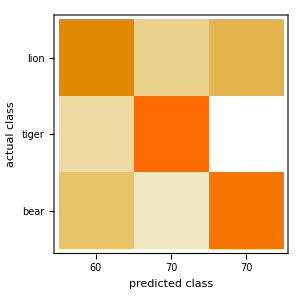

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
Map[{#,result[First[#]]}&,validation]//Grid
```

-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→bear | lion
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→lion | bear
-Graphics-→tiger | tiger
-Graphics-→bear | lion
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→lion | lion
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→lion | bear
-Graphics-→tiger | tiger
-Graphics-→bear | lion
-Graphics-→lion | bear
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→lion | tiger
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→lion | lion
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→lion | bear
-Graphics-→tiger | tiger
-Graphics-→lion | bear
-Graphics-→tiger | tiger
-Graphics-→bear | lion
-Graphics-→bear | lion
-Graphics-→tiger | tiger
-Graphics-→lion | bear
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→lion | bear
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→lion | bear
-Graphics-→lion | tiger
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→bear | lion
-Graphics-→bear | tiger
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→bear | tiger
-Graphics-→bear | bear
-Graphics-→bear | lion
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→lion | bear
-Graphics-→bear | lion
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→tiger | lion
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→bear | lion
-Graphics-→tiger | tiger
-Graphics-→lion | bear
-Graphics-→bear | tiger
-Graphics-→tiger | lion
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→lion | tiger
-Graphics-→lion | lion
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→tiger | lion
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→tiger | lion
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→tiger | lion
-Graphics-→lion | lion
-Graphics-→lion | tiger
-Graphics-→bear | lion
-Graphics-→lion | lion
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→bear | lion
-Graphics-→lion | tiger
-Graphics-→lion | tiger
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→lion | tiger
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→lion | bear
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→bear | lion
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→tiger | lion
-Graphics-→bear | bear
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→lion | lion
-Graphics-→bear | tiger
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→bear | lion
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→lion | bear
-Graphics-→tiger | tiger
-Graphics-→lion | tiger
-Graphics-→bear | bear
-Graphics-→lion | lion
-Graphics-→tiger | lion
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→bear | bear
-Graphics-→lion | lion
-Graphics-→lion | bear
-Graphics-→lion | lion
-Graphics-→tiger | lion
-Graphics-→lion | lion
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→bear | lion
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→lion | bear
-Graphics-→tiger | tiger
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→tiger | tiger
-Graphics-→tiger | tiger
-Graphics-→lion | bear
-Graphics-→bear | bear
-Graphics-→lion | tiger
-Graphics-→lion | lion
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→bear | bear
-Graphics-→lion | bear